### Import data from files

Note: On Windows computers, the file locations might need to be adjusted to include double forward slashes (//) instead of (/).
To change between “versions” (i.e. initial cell configurations), change  “v1” (ICC.1) to “v2” (ICC.2) or “v3” (ICC.3) in the next three lines.

```mathematica
datafilelocationNoDrug=StringJoin[ParentDirectory[NotebookDirectory[]],"/cumulant_data/v1/no_drug_time_0_to_200/"];
datafilelocationMFPMDrug=StringJoin[ParentDirectory[NotebookDirectory[]],"/cumulant_data/v1/mfpm_drug_time_200_to_350/"];
datafilelocationSCMDrug=StringJoin[ParentDirectory[NotebookDirectory[]],"/cumulant_data/v1/scm_drug_time_200_to_350/"];
```

```mathematica
density1predoses=Import[StringJoin[datafilelocationNoDrug,"u1_tracks_1.csv"],"csv"];
density2predoses=Import[StringJoin[datafilelocationNoDrug,"u1_tracks_2.csv"],"csv"];
density1dosesMFPM=Import[StringJoin[datafilelocationMFPMDrug,"u1_tracks_1_MFPMdrug.csv"],"csv"];
density2dosesMFPM=Import[StringJoin[datafilelocationMFPMDrug,"u1_tracks_2_MFPMdrug.csv"],"csv"];
density1dosesSCM=Import[StringJoin[datafilelocationSCMDrug,"u1_tracks_1_SCMdrug.csv"],"csv"];
density2dosesSCM=Import[StringJoin[datafilelocationSCMDrug,"u1_tracks_2_SCMdrug.csv"],"csv"];
```

### Join pre and post drug data. Then plot density dynamics.

Note: You might need to adjust PlotRanges for better overview.

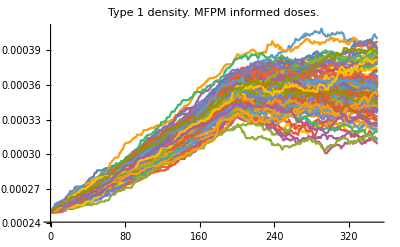

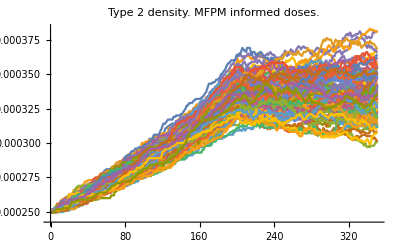

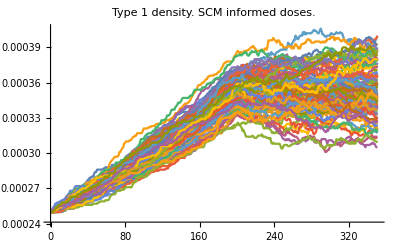

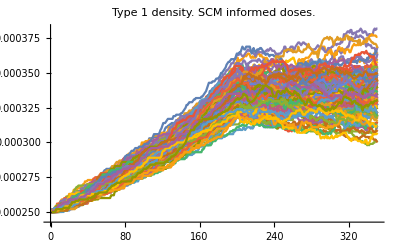

```mathematica
t1mfpm=Table[Join[density1predoses[[run]],density1dosesMFPM[[run]]],{run,1,100}];
t2mfpm=Table[Join[density2predoses[[run]],density2dosesMFPM[[run]]],{run,1,100}];t1scm=Table[Join[density1predoses[[run]],density1dosesSCM[[run]]],{run,1,100}];
t2scm=Table[Join[density2predoses[[run]],density2dosesSCM[[run]]],{run,1,100}];

d11mfpm=ListLinePlot[t1mfpm,PlotLabel->"Type 1 density. MFPM informed doses."]
d12mfpm=ListLinePlot[t2mfpm,PlotLabel->"Type 2 density. MFPM informed doses."]
d11scm=ListLinePlot[t1scm,PlotLabel->"Type 1 density. SCM informed doses."]
d12scm=ListLinePlot[t2scm,PlotLabel->"Type 1 density. SCM informed doses."]
```